## τα from fitting CRSISF, SISF to stretched exponential

```mathematica
(*saveFolder="/Users/chengling/Learning/Research/TempDirForRemote/p380TauAlpha/N4096/";*)
```

```mathematica
saveFolder="/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825";
```

```mathematica
p0=3.825
```

3.825

```mathematica
Directory[]
```

/home/chengling

```mathematica
stretchedExp[t_,G_,τ_,β_]:=G Exp[-(t/τ)^β];
```

```mathematica
nestedArray={{{True,False},{False,True},{True,True}}};
falseIndices=Position[nestedArray,False,{3},Heads->False]
```

{{1,1,2},{1,2,1}}

```mathematica
list[[1,1,1]]
```

23

```mathematica
list={{{23,2},{4,6}},{{25,8},{4,78}},{{26,4185},{4,4}}};
indicesToDelete={{1,1,1}};
result=Delete[list,List/@indicesToDelete]
```

Delete::psl: Position specification {1,1,1} in {{{23,2},{4,6}},{{25,8},{4,78}},{{26,4185},{4,4}}} is not a machine-sized integer or a list of machine-sized integers.

Delete[{{{23,2},{4,6}},{{25,8},{4,78}},{{26,4185},{4,4}}},{{{1,1,1}}}]

## Data reading

```mathematica
saveFolders={"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.825","/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800","/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.750"};
```

```mathematica
p0s={3.825,3.8,3.75}
```

{3.825,3.8,3.75}

```mathematica
temperatures={{0.063 ,0.039, 0.03105, 0.016 ,0.01, 0.008, 0.0063, 0.005 ,0.00385, 0.0031, 0.0025, 0.002, 0.0015, 0.001, 0.00067 ,0.0005},{0.063 ,0.039 ,0.03105, 0.025, 0.016 ,0.01 ,0.008 ,0.0063, 0.005, 0.00385, 0.0031, 0.0028 ,0.0025 ,0.0022},{0.063, 0.039, 0.03105, 0.025 ,0.02, 0.016, 0.014,0.012 ,0.011, 0.01, 0.0093}};
 records={{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19},{10, 11, 12 ,13, 14 ,15 ,16, 17 ,18 ,19}};
tauEstimate={{1, 2, 4 ,9 ,15,25, 40 ,60, 80, 120,200 ,300 ,1000 ,1500, 5000,10000},{1, 3, 4 ,8 ,15,40 ,70 ,150 ,250, 600 ,2000, 2500 ,4500, 9500},{4 ,5 ,7 ,10 ,30 ,70, 150 ,700,1400, 4000 ,9500}}
(*tauEstimate={{1., 2., 4. ,9. ,15. ,25., 40. ,60., 80., 120. ,200. ,300. ,1000. ,1500., 5000. ,10000.},{1., 3., 4. ,8. ,15. ,40. ,70. ,150. ,250., 600. ,2000., 2500. ,4500., 9500.},{4. ,5. ,7. ,10. ,30. ,70., 150. ,700. ,1400., 4000. ,9500.}};*)
```

{{1,2,4,9,15,25,40,60,80,120,200,300,1000,1500,5000,10000},{1,3,4,8,15,40,70,150,250,600,2000,2500,4500,9500},{4,5,7,10,30,70,150,700,1400,4000,9500}}

```mathematica
overlapCRoverlap=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/overlapCRoverlap_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/overlapCRoverlap_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

```mathematica
SISFCRSISF=Table[Table[DeleteCases[Table[Import[dataNameStringNumber[{"/home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p","/SISFCRSISF_N4096_p","_T","_waitingTime","_idx",".nc"},{p0s[[p]],p0s[[p]],temperatures[[p,T]],If[tauEstimate[[p,T]]<1000,10000,tauEstimate[[p,T]]*10],records[[p,i]]},{3,4,8,0,0}],"Data"],{i,Length[records[[p]]]}],$Failed],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx14.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx15.nc not found during Import.

Import::nffil: File /home/chengling/Research/Project/Cell/glassyDynamics/N4096/tauAlphaData/p3.800/SISFCRSISF_N4096_p3.8000_T0.06300000_waitingTime10000_idx17.nc not found during Import.

General::stop: Further output of Import::nffil will be suppressed during this calculation.

Import::format: Cannot import data as Data.

```mathematica
CRoverlapMean=Table[Table[Table[Mean[DeleteCases[Table[overlapCRoverlap[[p,T,i,2,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
overlapMean=Table[Table[Table[Mean[DeleteCases[Table[overlapCRoverlap[[p,T,i,1,rec]],{i,Length[overlapCRoverlap[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[overlapCRoverlap[[p,T,i,1]]],{i,Length[overlapCRoverlap[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
CRSISFMean=Table[Table[Table[Mean[DeleteCases[Table[SISFCRSISF[[p,T,i,2,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,2]]],{i,Length[SISFCRSISF[[p,T]]]}]]-3}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
SISFMean=Table[Table[Table[Mean[DeleteCases[Table[SISFCRSISF[[p,T,i,1,rec]],{i,Length[SISFCRSISF[[p,T]]]}],_Missing|_Part|0.]],{rec,Max[Table[Length[SISFCRSISF[[p,T,i,1]]]-3,{i,Length[SISFCRSISF[[p,T]]]}]]}],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

Part::partw: Part 104 of … does not exist.

Part::partw: Part 105 of … does not exist.

Part::partw: Part 106 of … does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
time={0.,0.00999999999476131,0.01999999998952262,0.02999999998428393,0.03999999997904524,0.04999999997380655,0.05999999996856786,0.06999999996332917,0.07999999995809048,0.0899999999528518,0.0999999999476131,0.10999999994237442,0.12999999993189704,0.13999999992665835,0.15999999991618097,0.1799999999057036,0.1999999998952262,0.21999999988474883,0.24999999986903276,0.2799999998533167,0.31999999983236194,0.34999999981664587,0.3999999997904524,0.449999999764259,0.4999999997380655,0.5599999997066334,0.6299999996699626,0.709999999628053,0.7899999995861435,0.8899999995337566,0.999999999476131,1.1199999994132668,1.2599999993399251,1.4099999992613448,1.579999999172287,1.7799999990675133,1.999999998952262,2.2399999988265336,2.509999998685089,2.8199999985226896,3.159999998344574,3.5499999981402652,3.9799999979150016,4.469999997658306,5.009999997375417,5.6199999970558565,6.309999996694387,7.079999996291008,7.9399999958404806,8.909999995332328,9.99999999476131,11.21999999412219,12.58999999340449,14.129999992597732,15.849999991696677,17.77999999068561,19.949999989548814,22.389999988270574,25.119999986840412,28.179999985237373,31.619999983435264,35.47999998141313,39.80999997914478,44.669999976598774,50.11999997374369,56.22999997054285,63.09999996694387,70.78999996291532,79.42999995838909,89.12999995330756,99.9999999476131,112.1999999412219,125.88999993405014,141.2499999260035,158.489999916972,177.82999990684038,199.52999989547243,223.86999988272146,251.18999986840936,281.8399998523528,316.2299998343369,354.80999981412606,398.10999979144253,446.6799997659982,501.1899997374421,562.3399997054075,630.9599996694596,707.949999629127,794.3299995838752,891.2499995331018,999.999999476131,1122.0199994122086,1258.9299993404857,1412.5399992600142,1584.8899991697253,1778.2799990684143,1995.2599989547452,2238.719998827204,2511.889998684099,2818.3799985235382,3162.2799983433797,3548.129998141245,3981.069997914441,4466.839997659961,5011.869997374437,5623.40999705407,6309.569996694612,7079.459996291291,7943.279995838762,8912.509995331013,9999.99999476131,11220.179994122096,12589.249993404883,14125.379992600152,15848.929991697238,17782.78999068415,19952.619989547442,22387.209988272036,25118.85998684101,28183.829985235367,31622.779984235283,35481.33998782885,39810.7199918609,44668.35999638493,50118.72000146097,56234.13000715639,63095.73001354675,70794.58002071686,79432.82002876185,89125.09003778848,100000.00004791653}
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,3162.28,3548.13,3981.07,4466.84,5011.87,5623.41,6309.57,7079.46,7943.28,8912.51,10000.,11220.2,12589.2,14125.4,15848.9,17782.8,19952.6,22387.2,25118.9,28183.8,31622.8,35481.3,39810.7,44668.4,50118.7,56234.1,63095.7,70794.6,79432.8,89125.1,100000.}

```mathematica
Flatten[Normal[test2[[4]]]]-test2[[4,1,1]]
```

{0.,0.01,0.02,0.03,0.04,0.05,0.06,0.07,0.08,0.09,0.1,0.11,0.13,0.14,0.16,0.18,0.2,0.22,0.25,0.28,0.32,0.35,0.4,0.45,0.5,0.56,0.63,0.71,0.79,0.89,1.,1.12,1.26,1.41,1.58,1.78,2.,2.24,2.51,2.82,3.16,3.55,3.98,4.47,5.01,5.62,6.31,7.08,7.94,8.91,10.,11.22,12.59,14.13,15.85,17.78,19.95,22.39,25.12,28.18,31.62,35.48,39.81,44.67,50.12,56.23,63.1,70.79,79.43,89.13,100.,112.2,125.89,141.25,158.49,177.83,199.53,223.87,251.19,281.84,316.23,354.81,398.11,446.68,501.19,562.34,630.96,707.95,794.33,891.25,1000.,1122.02,1258.93,1412.54,1584.89,1778.28,1995.26,2238.72,2511.89,2818.38,-40000.}

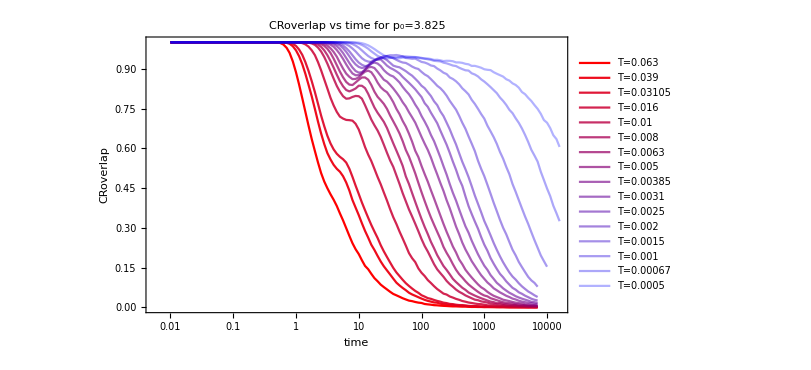
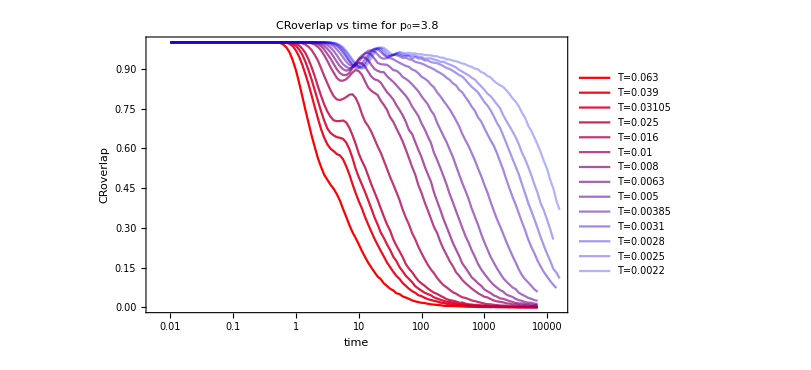
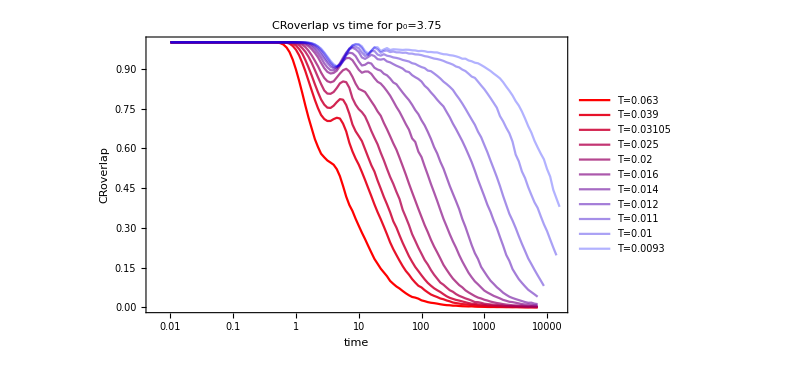

```mathematica
CRoverlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRoverlapMean[[p,T,rec]]},{rec,Length[CRoverlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRoverlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRoverlapPlots]
```

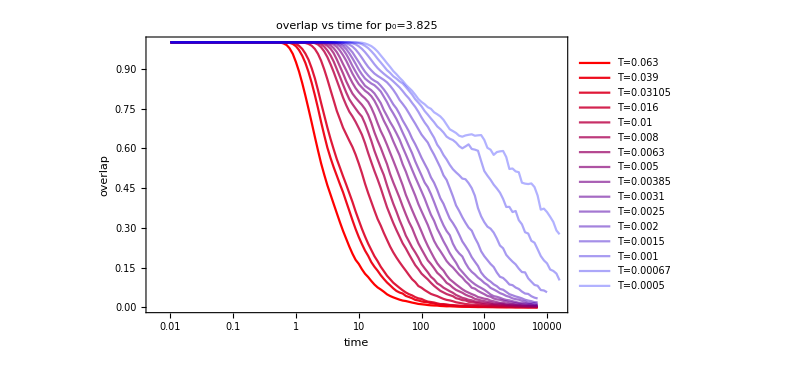
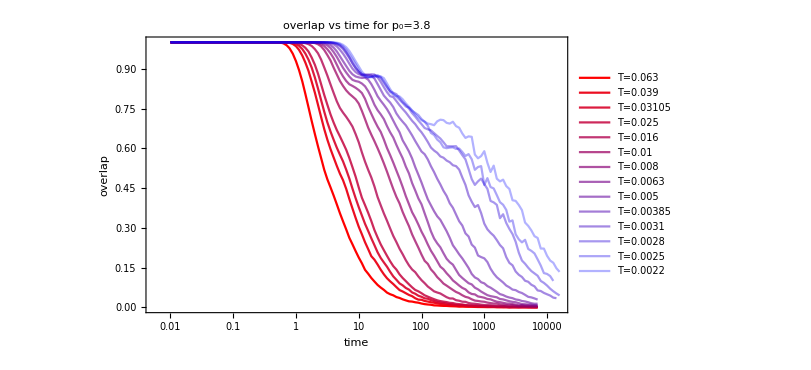
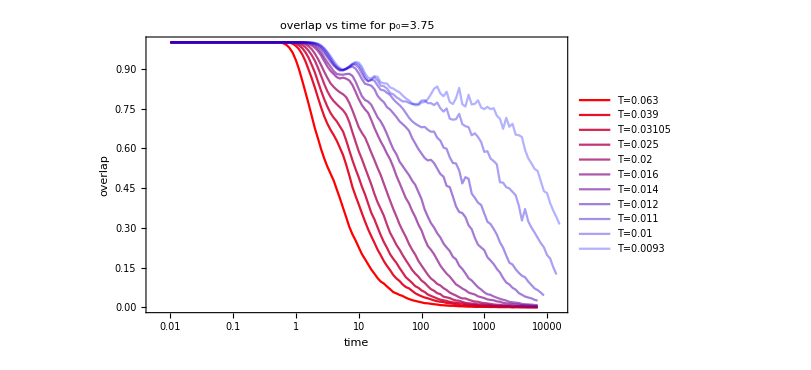

```mathematica
overlapPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],overlapMean[[p,T,rec]]},{rec,Length[overlapMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","overlap"},ImageSize->600,PlotLabel->"overlap vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[overlapPlots]
```

```mathematica
overlapCRoverlap[[3,10,1]]
```

<|/firstValue→NumericArray[…],/secondValue→NumericArray[…]|>

```mathematica
sisfCRSISF[[3,10,1]]
```

<|/firstValue→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{96}],/secondValue→NetCDFTools`Private`postProcessDataArray[Real64,$Failed,{96}]|>

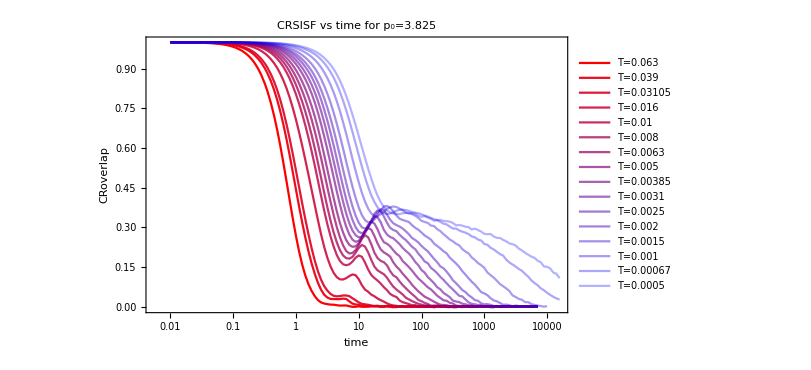
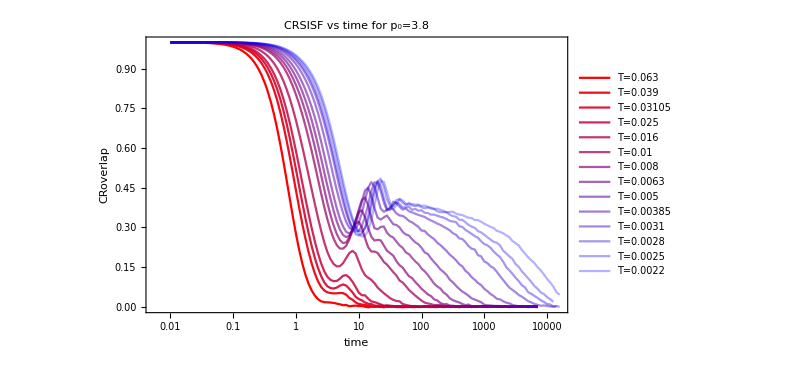
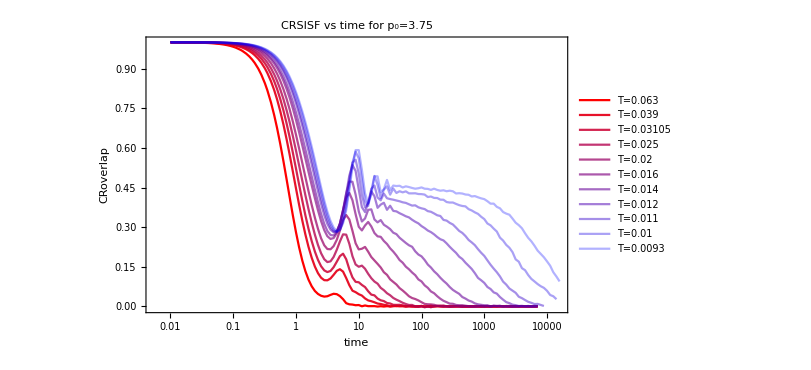

```mathematica
CRSISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],CRSISFMean[[p,T,rec]]},{rec,Length[CRSISFMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","CRoverlap"},ImageSize->600,PlotLabel->"CRSISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[CRSISFPlots]
```

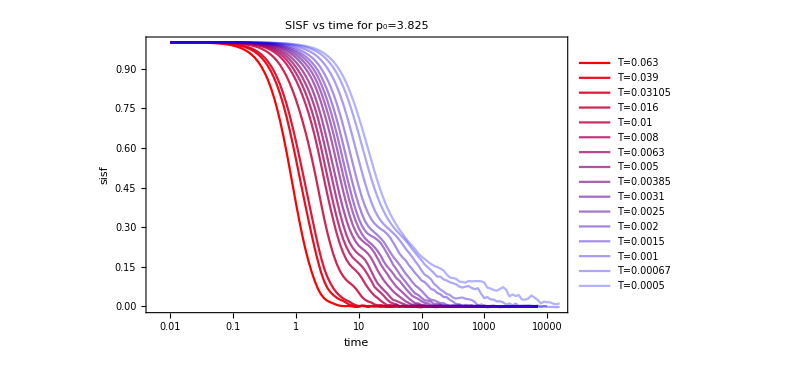
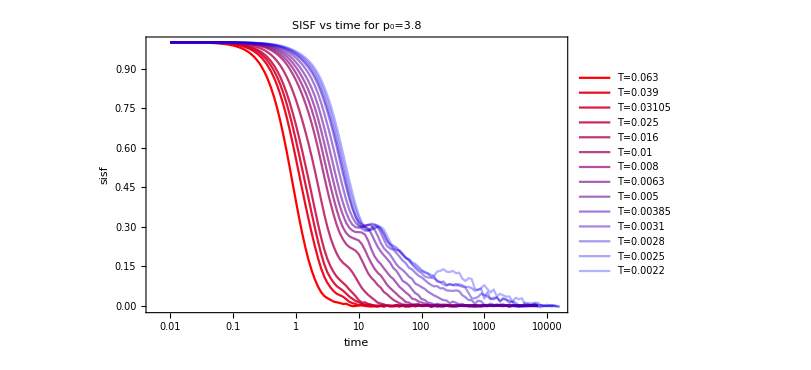
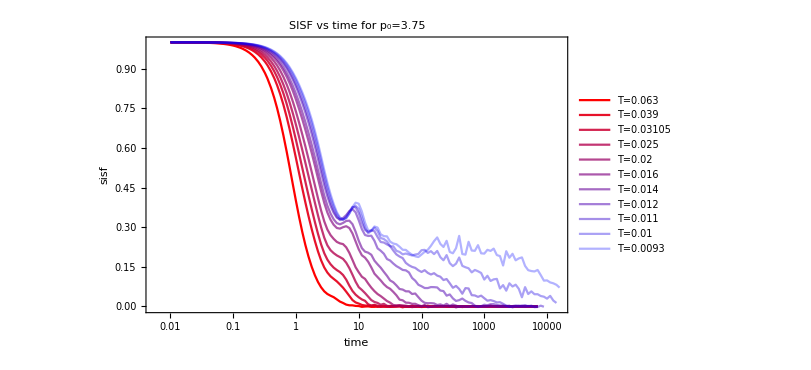

```mathematica
SISFPlots=Table[
ListLogLinearPlot[Table[Table[{time[[rec]],SISFMean[[p,T,rec]]},{rec,Length[sisfMean[[p,T]]]}],{T,Length[temperatures[[p]]]}],PlotLegends->Table["T="<>ToString[temperatures[[p]][[T]]],{T,Length[temperatures[[p]]]}],PlotStyle->redBluePlotConfig[Length[temperatures[[p]]]],FrameLabel->{"time","sisf"},ImageSize->600,PlotLabel->"SISF vs time for p_0="<>ToString[p0s[[p]]],Joined->True],{p,Length[p0s]}];
Column[SISFPlots]
```

```mathematica
fitStartPosNumCRoverlap={{5.10626766220749,7.33191538251281,8.55985787911546,12.2784340567836,19.9072886965551,25.7889817991537,30.637337279973,37.6842190674617,45.5543099631693,50.5020197714363,62.1221406262914,68.8808652860745,67.6591820810754,63.1059743291918,65.3198992057935,65.3198992057935},{5.01478428760811,7.32441666499497,8.5513871706197,10.1576883700357,15.0926921537208,26.2127397674524,34.5438457528856,43.9739661001025,55.9859322143738,65.3667696373491,73.7426031413621,77.6531507838861,78.9942616149603,80.3639303419727},{5.70091979646235,9.9139176390011,13.0736090674479,15.8124348238313,22.3453150952929,27.9774746328855,32.6883493871117,35.6401829658425,40.9274813028465,42.3675930783094,42.3675930783094}};
fitStartPosNumCRSISF={{3.82593901080345,6.42514329029143,7.50544226387184,12.1733886785023,15.4940210355944,18.0947102522978,21.8739684327274,23.4273310457724,26.4268957401349,27.818391638738,32.4911384324115,36.658872587844,47.4988792633103,58.429105486656,62.6045861978669,62.602403789757},{4.73460222993003,6.70473259683864,7.57481345968491,8.42168848912098,12.7747567053411,24.3367808834003,28.0136577418138,35.1825122824413,44.1982670270607,50.8616639330646,60.5891221161582,62.756131030346,65.0278968206533,66.1713167215838},{6.49381631576212,7.98913941667404,9.82878873000032,12.5169927303173,14.6217717445672,19.6110117547605,26.3026799189538,41.209751909733,44.1570447353312,47.315125896148,46.5050376166607}};
```

```mathematica
fitStartPosCRoverlap=Table[Table[Position[time,_?(#>fitStartPosNumCRoverlap[[p,i]]&)][[1,1]],{i,Length[fitStartPosNumCRoverlap[[p]]]}],{p,Length[p0s]}];
fitStartPosCRSISF=Table[Table[Position[time,_?(#>fitStartPosNumCRSISF[[p,i]]&)][[1,1]],{i,Length[fitStartPosNumCRSISF[[p]]]}],{p,Length[p0s]}];
```

### fitting CRoverlap

```mathematica
fitsCROverlap=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRoverlapMean[[p,T,rec]]]},{rec,fitStartPosCRoverlap[[p,T]],Length[CRoverlapMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitsCROverlap[[1,1]]
```

FittedModel[0.989939 ⅇ^(-0.475642 t^0.519386)]

```mathematica
tauCROverlapfits=Table[Table[fitsCROverlap[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{4.18165,8.80892,12.5864,33.9048,68.8421,95.7949,139.814,199.292,307.14,437.983,654.612,941.88,1673.6,4228.43,14267.8,43908.5},{5.30278,11.4021,16.643,23.8237,53.982,135.937,215.218,375.12,683.414,1472.1,3540.34,5833.45,9135.65,17015.6},{7.55403,19.9625,31.6152,53.9032,98.0561,214.741,408.815,1253.78,2568.72,7378.46,16491.8}}

```mathematica
CRoverlapFittingPlots=Table[Show[CRoverlapPlots[[p]],Table[LogLinearPlot[fitsCROverlap[[p,T]][x],{x,time[[fitStartPosCRoverlap[[p,T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

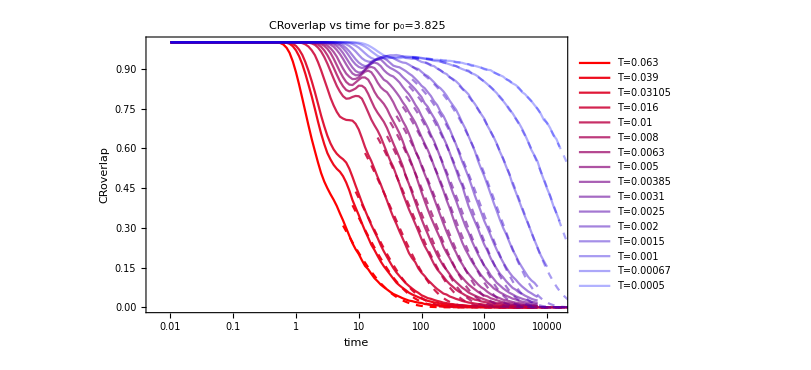
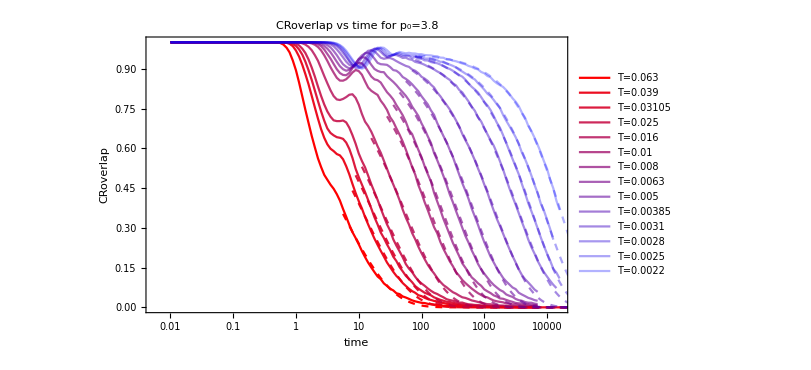
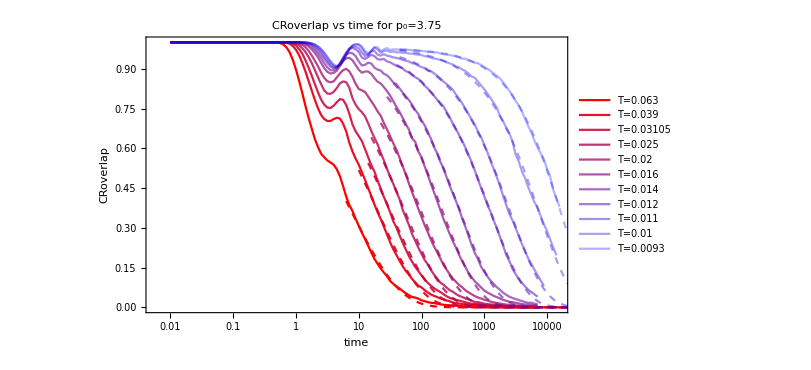

```mathematica
Column[CRoverlapFittingPlots]
```

### fitting CRSISF

```mathematica
fitsCRSISF=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[CRSISFMean[[p,T,rec]]]},{rec,fitStartPosCRSISF[[p,T]],Length[CRSISFMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
fitsCROverlap[[1,1]]
```

FittedModel[0.989939 ⅇ^(-0.475642 t^0.519386)]

```mathematica
tauCRSISFfits=Table[Table[fitsCRSISF[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.50164,1.30537,1.60869,9.11748,17.8553,25.7028,35.1489,44.0346,65.9306,101.264,142.277,216.302,396.956,885.78,3331.77,11914.6},{1.30559,1.8089,1.81657,2.44833,11.4747,37.8226,53.1649,105.909,183.74,423.998,1316.26,2417.29,3517.23,7279.7},{1.18824,5.38219,5.62021,11.042,18.562,54.115,141.714,583.858,1288.76,3856.14,9853.81}}

```mathematica
CRSISFFittingPlots=Table[Show[CRSISFPlots[[p]],Table[LogLinearPlot[fitsCRSISF[[p,T]][x],{x,time[[fitStartPosCRSISF[[p,T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

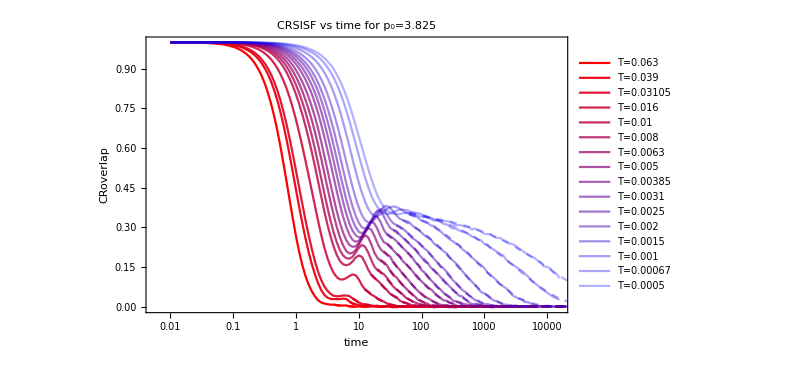
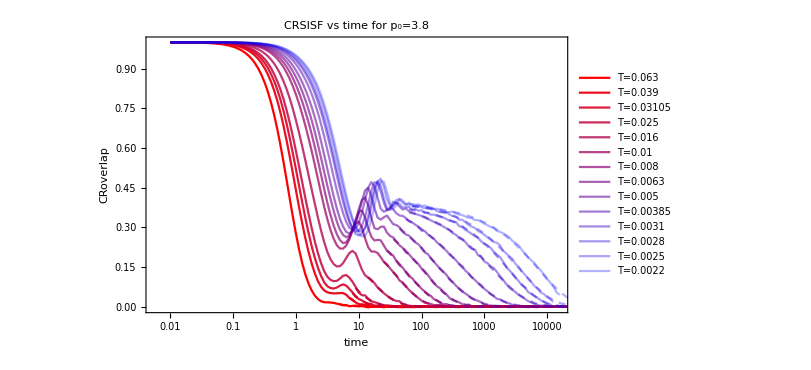
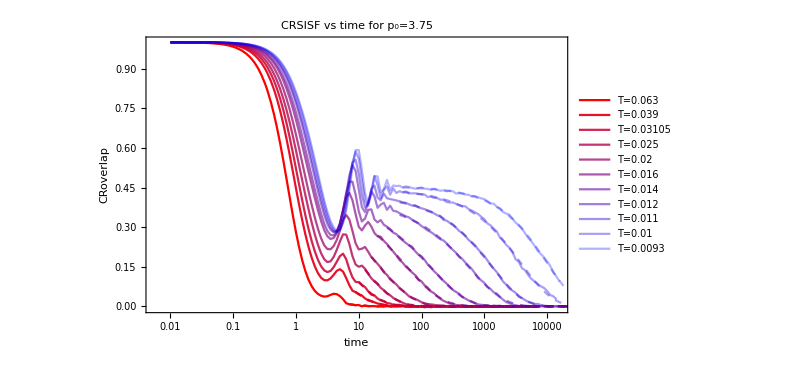

```mathematica
Column[CRSISFFittingPlots]
```

### fitting SISF

```mathematica
fitsSISF=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[SISFMean[[p,T,rec]]]},{rec,fitStartPosCRSISF[[p,T]],Length[SISFMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
tauSISFfits=Table[Table[fitsSISF[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{0.846914,1.3329,1.6508,4.11758,6.30733,8.71911,9.13446,18.3102,23.8123,30.1846,15.5289,31.4755,39.2811,21.5245,14.4679,8.92874},{1.22099,1.6842,2.46904,2.61797,4.61847,11.3738,17.8135,28.2914,40.4117,29.8244,61.3254,41.6136,52.0804,1288.16},{1.25001,1.68704,3.322,3.47112,9.57624,19.501,18.328,16.9515,226.118,1722.93,13161.9}}

```mathematica
SISFFittingPlots=Table[Show[SISFPlots[[p]],Table[LogLinearPlot[fitsSISF[[p,T]][x],{x,time[[fitStartPosCRSISF[[p,T]]]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

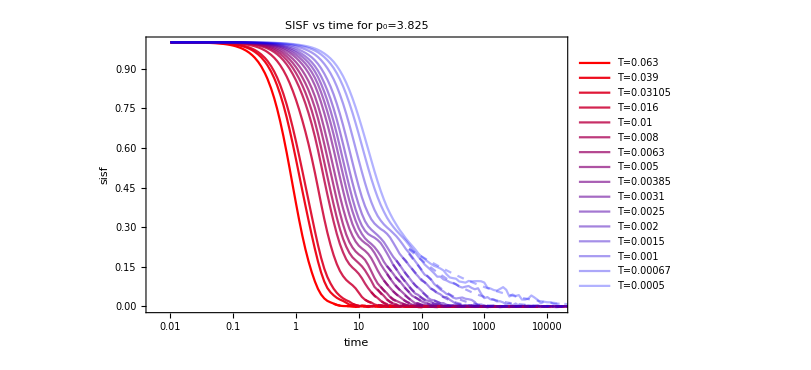
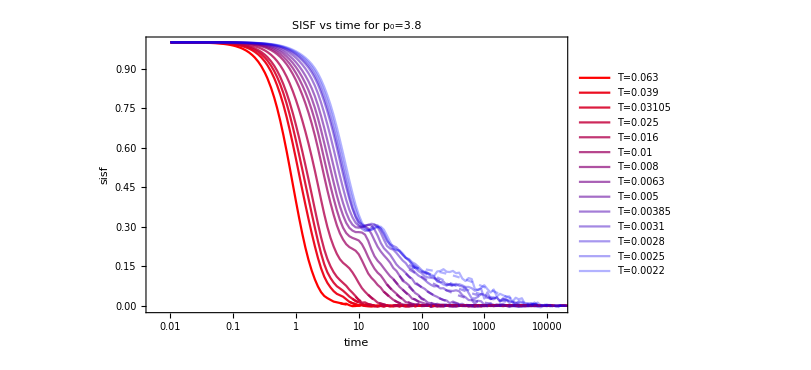
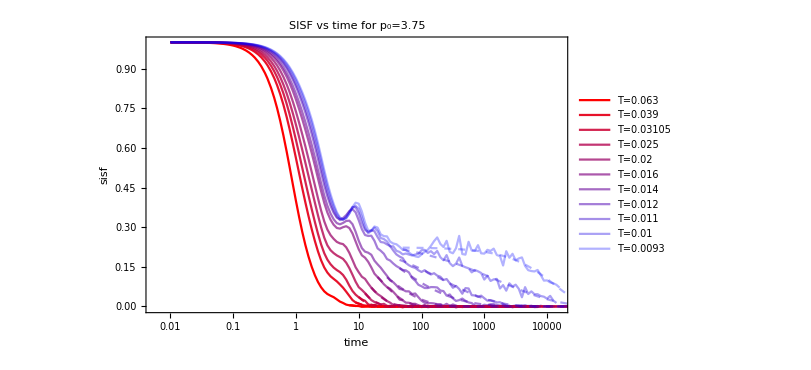

```mathematica
Column[SISFFittingPlots]
```

### fitting overlap

```mathematica
fitsoverlap=Table[Table[NonlinearModelFit[Table[{Normal[time[[rec]]],Normal[overlapMean[[p,T,rec]]]},{rec,fitStartPosCRoverlap[[p,T]]+7,Length[overlapMean[[p,T]]]}],{stretchedExp[t,G,τ,β],{0.99>β>0.2,0.99>G>0,τ>0.5}},{G,τ,β},t],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}];
```

```mathematica
tauoverlapfits=Table[Table[fitsoverlap[[p,T]]["BestFitParameters"][[2,2]],{T,Length[temperatures[[p]]]}],{p,Length[p0s]}]
```

{{1.93792,3.56417,4.87154,13.0594,22.1632,27.3529,41.1166,57.3496,80.7466,120.083,168.715,250.081,431.535,877.76,4343.45,16440.4},{2.19225,4.61007,6.54948,8.88305,18.0084,39.2704,59.9263,92.4162,153.623,332.944,855.644,2491.1,4072.95,5069.88},{2.98774,6.24631,9.76172,17.1542,28.741,65.4188,118.005,501.132,1111.8,5109.64,15889.8}}

```mathematica
overlapFittingPlots=Table[Show[overlapPlots[[p]],Table[LogLinearPlot[fitsoverlap[[p,T]][x],{x,time[[fitStartPosCRoverlap[[p,T]]+7]],100000},PlotRange->{{0.01,10000},{0,1}},PlotStyle->{Dashed,redBluePlotConfig[Length[temperatures[[p]]]][[T]]}],{T,Length[temperatures[[p]]]}]],{p,Length[p0s]}];
```

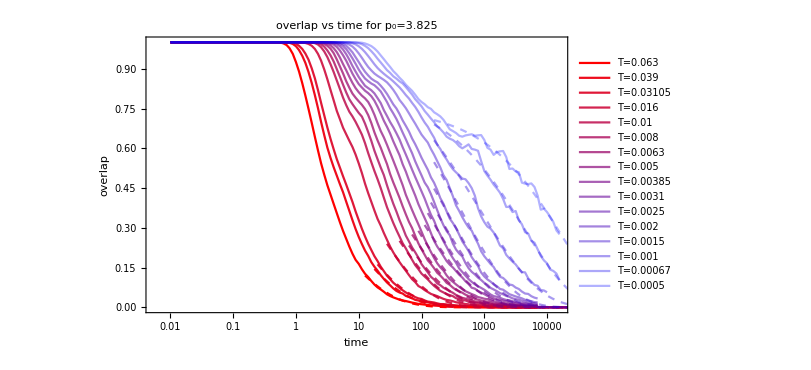
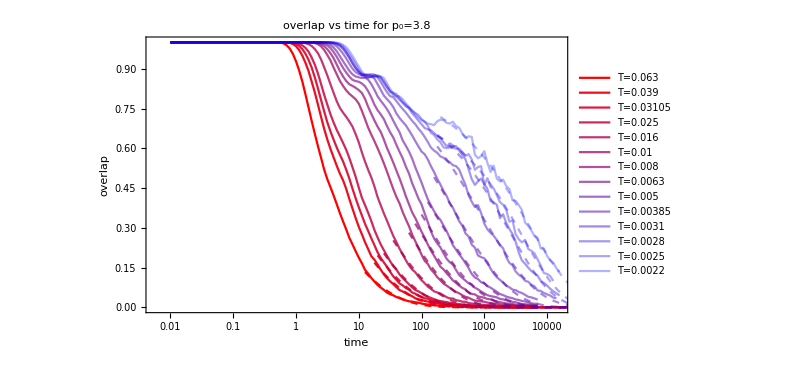
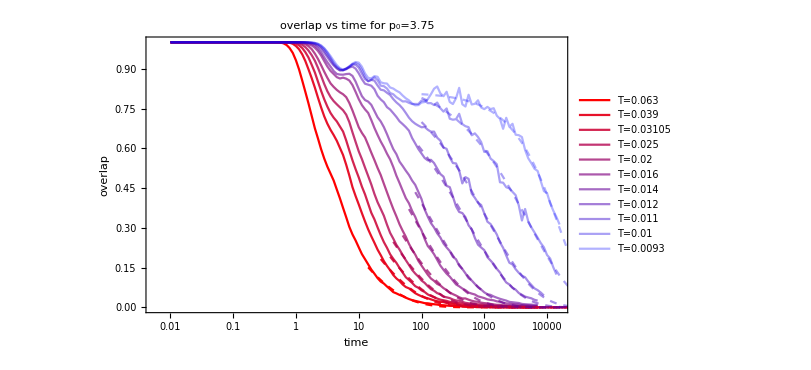

```mathematica
Column[overlapFittingPlots]
```

#### Tau Alphas

```mathematica
tauAlphafitingPlot=Table[ListLogPlot[{Table[{1/temperatures[[p,T]],tauCROverlapfits[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauCRSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauoverlapfits[[p,T]]},{T,Length[temperatures[[p]]]}],Table[{1/temperatures[[p,T]],tauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}]},FrameLabel->{"1/T","τα"},PlotLegends->{"CRoverlapFunction","CRSISF","overlapFunction","SISF"},PlotMarkers->{Style["■",Large],Style["●",Large],Style["□",Large],Style["○",Large]},ImageSize->600,PlotLabel->"p_0="<>ToString[p0s[[p]]]<>" τα vs 1/T",Joined->True,PlotRange->All],{p,Length[p0s]}];
```

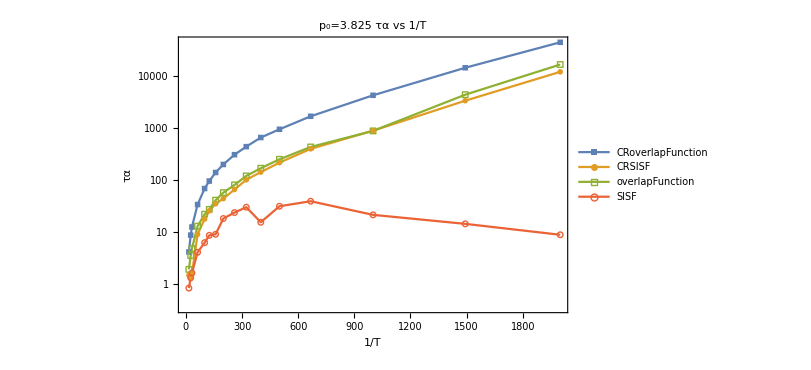
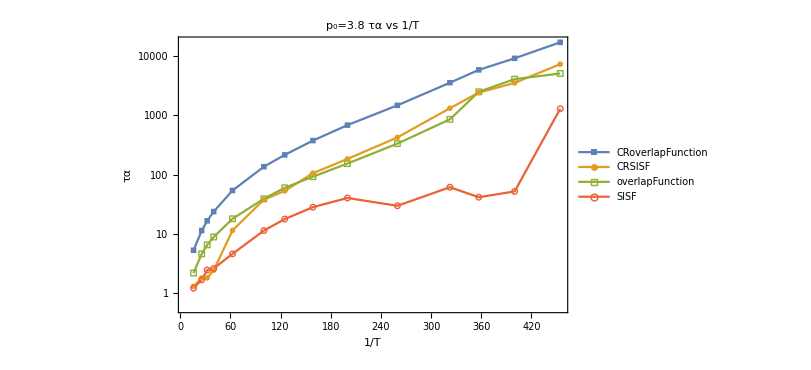
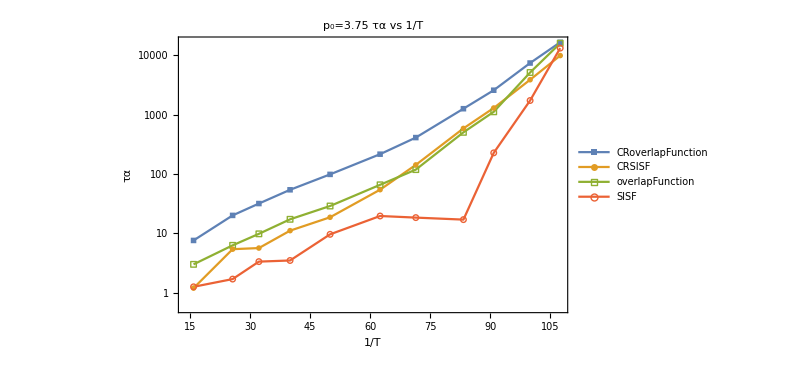

```mathematica
Column[tauAlphafitingPlot]
```

```mathematica
tauTables=Table[Prepend[Table[{temperatures[[p,T]],tauCRSISFfits[[p,T]],tauCROverlapfits[[p,T]],tauoverlapfits[[p,T]],tauSISFfits[[p,T]]},{T,Length[temperatures[[p]]]}],{"T","τα CRSISF","τα CR overlap","τα SISF","τα overlap"}],{p,Length[p0s]}];
```

```mathematica
ToString[NumberForm[p0s[[1]],{5,3}]]
```

3.825

```mathematica
Table[Export["/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP"<>ToString[NumberForm[p0s[[p]],{5,3}]]<>"_Over10conf.csv",tauTables[[p]],"CSV"],{p,Length[p0s]}]
```

{/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.825_Over10conf.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.800_Over10conf.csv,/home/chengling/Research/Project/Cell/glassyDynamics/plots/tauAlpha/tauAlphaTableP3.750_Over10conf.csv}